```mathematica
E1,Ax, Ay,A,generatePlotAndRoots,pxValues,pyValues,newResults,results,tsExtended,validData,realAndImagTimes,colorFunction,coloredPointsPx, coloredPointsPy]

(*Define the electric field function as a 2D vector*)
E1[t_]:={Cos[Pi/4] Cos[t]-Sin[Pi/4] Cos[2 t],0};

(*Define the vector potential components*)
Ax[tx_]:=-Integrate[E1[t][[1]],t]/. t->tx;
Ay[tx_]:=-Integrate[E1[t][[2]],t]/. t->tx;

(*Define the 2D vector potential A*)
A[tx_]:={Ax[tx],Ay[tx]};

(*Function to generate plots and roots for given px and py*)
generatePlotAndRoots[px_,py_]:=Module[{Ip=0.5,Sf,Sfunc,DsFunc,realMin,realMax,imagMin,imagMax,realSteps,imagSteps,listofseeds,allSolutions,complexSolutions,nonrepeatedSolutions,tValues,tolerance,filteredTValues,plotEx,plotEy,plotRoots,PlotExEy3D},

(*Define Sf,Sfunc,and DsFunc in terms of px,Ax,py,and Ay*)
Sf[tk_]:=Integrate[2 (px*Ax[t]+py*Ay[t])+(Ax[t]^2+Ay[t]^2),t]/. t->tk;
Sfunc[t_]:=0.5*Sf[t]+(0.5*(px^2+py^2)+Ip)*t;
DsFunc[t_]:=D[Sfunc[tc],tc]/. tc->t;

(*Generate the grid of seeds*)
realMin=-2.133;realMax=4.15;
imagMin=0;imagMax=5;
realSteps=10;imagSteps=5;
listofseeds=Flatten[
Table[
x+I y,{x,realMin,realMax,(realMax-realMin)/realSteps},{y,imagMin,imagMax,(imagMax-imagMin)/imagSteps}
],1];

(*Find roots*)
allSolutions=Round[t/. Quiet[
Table[
FindRoot[DsFunc[t]==0,{t,tseed}],
{tseed,listofseeds}]
],0.0001];

complexSolutions=Select[allSolutions,Im[#]>0&];
nonrepeatedSolutions=DeleteDuplicates[complexSolutions];
tValues=SortBy[Select[nonrepeatedSolutions,(Re[#]>=realMin&&Re[#]<=realMax)&],Re[#]&];

(*Define a tolerance for considering values as 0*)
tolerance=10^-3;
filteredTValues=Select[tValues,Abs[Re[DsFunc[#]]]<=tolerance&&Abs[Im[DsFunc[#]]]<=tolerance&];

(*Plot Ex and Ey*)
plotEx=Quiet[
Plot[E1[t][[1]],
{t,realMin,realMax},
PlotLabel->"px = "<>ToString[px]<>", py = "<>ToString[py],AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]
];

plotEy=Quiet[
Plot[E1[t][[2]],
{t,realMin,realMax},
PlotLabel->"px = "<>ToString[px]<>", py = "<>ToString[py],AxesLabel->{"Time, t","Electric Field Ey"},ImageSize->Large]
];

plotRoots=Quiet[
ListPlot[
{{Re[#],E1[Re[#]][[1]]}&/@filteredTValues},
PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]
];

(*Return both the plots and filteredTValues*)
{Show[plotEx,plotRoots,PlotRange->All],Show[plotEy,plotRoots,PlotRange->All],filteredTValues}
]


(*Electric field plot along with saddle points as red dots,and for the slider for px and py from-3 to 3.*)
Manipulate[
Module[
{plotData,plotEx,plotEy,plotRoots,filteredTValues},

plotData=generatePlotAndRoots[px,py];
plotEx=plotData[[1]];
plotEy=plotData[[2]];
filteredTValues=plotData[[3]];

plotRoots=ListPlot[
{{Re[#],E1[Re[#]][[1]]}&/@filteredTValues},
PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large];

Show[
plotEx,plotEy,plotRoots,PlotRange->All]],
{{px,0,"Momentum px"},-3,3,0.1},
{{py,0,"Momentum py"},-3,3,0.1}
]


Manipulate[Module[{plotData,filteredTValues,timeValues,exValues,eyValues,rootPoints},plotData=generatePlotAndRoots[px,py];
filteredTValues=plotData[[3]];
(*Extract time,Ex,and Ey values*)timeValues=Re[#]&/@filteredTValues;
exValues=E1[#][[1]]&/@timeValues;
eyValues=E1[#][[2]]&/@timeValues;
(*Create root points for plotting*)
rootPoints=Graphics3D[{Red,PointSize[Large],Point[Transpose[{exValues,eyValues,timeValues}]]}];
(*Create 3D plot*)
Show[
ParametricPlot3D[{E1[t][[1]],E1[t][[2]],t},{t,-2.133,4.15},
PlotStyle->{Blue},AxesLabel->{"Electric Field Ex","Electric Field Ey","Time, t"},PlotLabel->"px = "<>ToString[px]<>", py = "<>ToString[py]<>", 3D Electric Field Plot",ImageSize->{1200,600},PlotRange->All],
rootPoints,ImageSize->{1200,600}]
],{{px,0,"Momentum px"},-3,3,0.1},{{py,0,"Momentum py"},-3,3,0.1}]
```

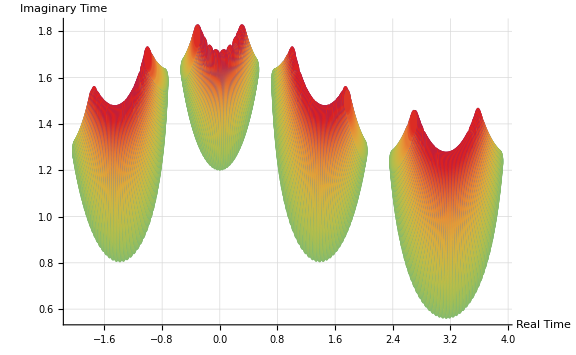

-Graphics3D-

```mathematica
ClearAll[pxValues,pyValues,newResults,results,tsExtended,validData,realAndImagTimes,colorFunction,coloredPointsPx, coloredPointsPy]

(*Define the range for px and py values*)
pxValues=Range[-3,3,0.1];
pyValues=Range[-3,3,0.1];

(*Generate results using the precise px and py values*)
results=Table[
generatePlotAndRoots[px,py],
{px,pxValues},{py,pyValues}
];

newResults=Flatten[
Table[
{pxValues=-3+(i-1)*0.1,
pyValues=-3+(j-1)*0.1,
results[[i,j,3]]}
,
{i,Length[results]},{j,Length[results[[1]]]}
],
1];

tsExtended=Map[Join[{#[[1]],#[[2]]},PadRight[#[[3]],4,Null]]&,newResults];

(*Filter and prepare the data for further processing*)
validData=
Select[
Flatten[
Table[
If[
tsExtended[[i,j+2]]=!=Null,

{Re[tsExtended[[i,j+2]]],
Im[tsExtended[[i,j+2]]],
tsExtended[[i,1]],
tsExtended[[i,2]]}
,
Nothing]
,{i,Length[tsExtended]}
,{j,1,4}],
1],
#[[1]]=!=Null&];

(*Extract real and imaginary times*)
realAndImagTimes=validData[[All,1;;2]];

(*Generate a 2D heatmap for px and py using the Rainbow color scheme*)
colorFunction[pxOrPy_]:=ColorData["Rainbow"][Rescale[pxOrPy,{-3,3}]];
(*Generate a list of colored points with the custom color function for px*)
coloredPointsPx=Table[{colorFunction[validData[[i,3]]],Point[validData[[i,1;;2]]]},{i,1,Length[validData]}];
(*Generate a list of colored points with the custom color function for py*)
coloredPointsPy=Table[{colorFunction[validData[[i,4]]],Disk[validData[[i,1;;2]],0.05]},{i,1,Length[validData]}];
(*Plot the 2D graph with the custom color grading for px and py*)
Show[Graphics[{coloredPointsPx},Axes->True,AxesLabel->{"Real Time","Imaginary Time"},GridLines->Automatic],Graphics[{coloredPointsPy}],PlotRange->All,ImageSize->Large,AspectRatio->1/GoldenRatio]

(*Plot the 3D graph with color representing py*)ListPointPlot3D[{#[[1]],#[[2]],#[[3]]}&/@validData,ColorFunction->Function[{x,y,z},ColorData["Rainbow"][Rescale[z,{-3,3}]]],ColorFunctionScaling->False,AxesLabel->{"Real Time","Imaginary Time","px"},PlotLabel->"4D Data Representation",ImageSize->Large,PlotLegends->Placed[BarLegend[{"Rainbow",{-3,3}},LabelStyle->{FontSize->10},LegendLabel->"py"],{Right,Top}]]
```

### define functions

```mathematica
ClearAll[E1,Sf,Sfunc,Ax,Ay,E1,DsFunc,D2sFunc,px,py,t,action,timeA, timeB, timeC, timeD, psiA, Ip, prefactor, pxValues,pyValues, dataA, dataB,dataC,dataD,dataTotal];

Ip = 0.5;
prefactor = (ⅈ / Sqrt[π])*(2*Ip)^(1/4);
E1[t_]:={Cos[Pi/4] Cos[t]-Sin[Pi/4] Cos[2 t],0};
Ax[tx_]:=-Integrate[E1[t][[1]],t]/. t->tx;
Ay[tx_]:=-Integrate[E1[t][[2]],t]/. t->tx;
A[tx_]:={Ax[tx],Ay[tx]};
Sf[tk_,px_,py_]:=Integrate[2 (px*Ax[t]+py*Ay[t])+(Ax[t]^2+Ay[t]^2),t]/. t->tk;
Sfunc[t_,px_,py_]:=0.5*Sf[t,px,py]+(0.5*(px^2+py^2)+Ip)*t;
DsFunc[t_,px_,py_]:=D[Sfunc[tc,px,py],tc]/. tc->t;
D2sFunc[t_,px_,py_]:=0.057*D[Sfunc[tz,px,py],{tz,2}]/. tz->t;
action[t_,px_,py_]:=Exp[ⅈ*Sfunc[t,px,py]/0.057];

(*Selects time saddle point solutions for trajectory A,B,C,D individually and accordingly*)
timeA=Table[validData[[i]],{i,1,Length[validData],4}];
timeB=Table[validData[[i]],{i,2,Length[validData],4}];
timeC=Table[validData[[i]],{i,3,Length[validData],4}];
timeD=Table[validData[[i]],{i,4,Length[validData],4}];


(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj A*)
psiA =Table[
prefactor*action[
timeA[[i,1]]+ⅈ*timeA[[i,2]],timeA[[i,3]],timeA[[i,4]]
]*Sqrt[2π/(ⅈ *D2sFunc[
timeA[[i,1]]+ⅈ*timeA[[i,2]],timeA[[i,3]],timeA[[i,4]]])
],
{i,1,Length[timeA]}];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj B*)
psiB=Table[
prefactor*action[
timeB[[i,1]]+ⅈ*timeB[[i,2]],timeB[[i,3]],timeB[[i,4]]
]*Sqrt[2π/(ⅈ *D2sFunc[
timeB[[i,1]]+ⅈ*timeB[[i,2]],timeB[[i,3]],timeB[[i,4]]])
],
{i,1,Length[timeB]}];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj C*)
psiC=Table[
prefactor*action[
timeC[[i,1]]+ⅈ*timeC[[i,2]],timeC[[i,3]],timeC[[i,4]]
]*Sqrt[2π/(ⅈ *D2sFunc[
timeC[[i,1]]+ⅈ*timeC[[i,2]],timeC[[i,3]],timeC[[i,4]]])
],
{i,1,Length[timeC]}];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj C*)
psiD=Table[
prefactor*action[
timeD[[i,1]]+ⅈ*timeD[[i,2]],timeD[[i,3]],timeD[[i,4]]
]*Sqrt[2π/(ⅈ *D2sFunc[
timeD[[i,1]]+ⅈ*timeD[[i,2]],timeD[[i,3]],timeD[[i,4]]])
],
{i,1,Length[timeD]}];

(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj A+B+C+D*)
totalPsi =psiA+psiB +psiC +psiD;
```

Thread::tdlen: Objects of unequal length in {3.57689×10^-100+2.93855×10^-100 ⅈ,6.65837×10^-60+1.41576×10^-60 ⅈ,3.02109×10^-56+1.0368×10^-56 ⅈ,-1.5746×10^-50-1.86526×10^-50 ⅈ,8.91114×10^-48-1.01687×10^-47 ⅈ,5.32256×10^-45+1.57622×10^-45 ⅈ,7.02586×10^-43+1.54297×10^-42 ⅈ,-5.51253×10^-41+3.82824×10^-40 ⅈ,-1.27464×10^-69+8.76913×10^-70 ⅈ,-4.94792×10^-35-8.33709×10^-35 ⅈ,«3535»}+{«23»-«23» ⅈ,«9»,«3535»}+{«1»}+{-6.17515×10^-97+2.79109×10^-96 ⅈ,3.66405×10^-57+6.97915×10^-57 ⅈ,«8»,«3534»} cannot be combined.

### plotting

```mathematica
(*Define pxValues and pyValues range from-3 to 3 in increments of 0.5*)
pxValues=Range[-3,3,0.1];
pyValues=Range[-3,3,0.1];

(*Create data points for each psi*)
dataA=Table[{pxValues[[i]],pyValues[[j]],Abs[psiA[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataB=Table[{pxValues[[i]],pyValues[[j]],Abs[psiB[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataC=Table[{pxValues[[i]],pyValues[[j]],Abs[psiC[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataD=Table[{pxValues[[i]],pyValues[[j]],Abs[psiD[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];
dataTotal=Table[{pxValues[[i]],pyValues[[j]],Abs[totalPsi[[i]]]},{i,Length[pxValues]},{j,Length[pyValues]}];

(*Flatten the data points*)
dataA=Flatten[dataA,1];
dataB=Flatten[dataB,1];
dataC=Flatten[dataC,1];
dataD=Flatten[dataD,1];
dataTotal=Flatten[dataTotal,1];

(*Create 3D plots for each psi*)
ListLinePlot3D[{dataA,dataB,dataC,dataD,dataTotal},PlotStyle->{Red,Green,Blue,Orange,Black},AxesLabel->{"px","py","Magnitude of the spectral ionisation amplitude |ΨSPM|"},SphericalRegion->True,ScalingFunctions->{None,None,"Log"},ImageSize->{1200,600}]
```